```mathematica
normalDist[x_] = (1/Sqrt[2*Pi])*E^((-x^2)/2)
```

(ⅇ^(-x^2/2))/(√(2 π))

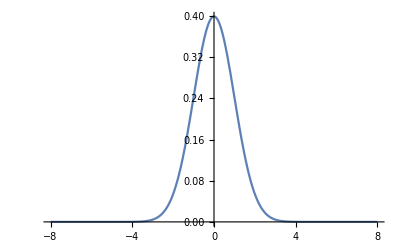

```mathematica
Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,-8,8}]
```

```mathematica
u1[z1_, q_] = Sqrt[q]*normalDist[z1]
u2[z1_, z2_, cPrev_, q_] = Sqrt[q]*(cPrev*normalDist[z1] + Sqrt[1 - cPrev^2]*normalDist[z2])
```

(ⅇ^(-z1^2/2) √q)/(√(2 π))

((cPrev ⅇ^(-z1^2/2))/(√(2 π))+(√(1-cPrev^2) ⅇ^(-z2^2/2))/(√(2 π))) √q

```mathematica
D[phi[u1[z1, q]]*phi[u2[z1, z2, cPrev, q]], cPrev]
```

((ⅇ^(-z1^2/2))/(√(2 π))-(cPrev ⅇ^(-z2^2/2))/(√(1-cPrev^2) √(2 π))) √q phi[(ⅇ^(-z1^2/2) √q)/(√(2 π))] phi'[((cPrev ⅇ^(-z1^2/2))/(√(2 π))+(√(1-cPrev^2) ⅇ^(-z2^2/2))/(√(2 π))) √q]

```mathematica
Intergrate[∫Phi[((cPrev ⅇ^(-z1^2/2))/(√(2 π))+(√(1-cPrev^2) ⅇ^(-z2^2/2))/(√(2 π))) √q] Phi[√5[z1]]ⅆz1,z2]
```

Intergrate[∫Phi[((cPrev ⅇ^(-z1^2/2))/(√(2 π))+(√(1-cPrev^2) ⅇ^(-z2^2/2))/(√(2 π))) √q] Phi[√5[z1]]ⅆz1,z2]

```mathematica
Function[cPrev,Intergrate[∫Phi[u1[z1]] Phi[u2[z1,z2,cPrev]]ⅆz1,z2]]
```

Function[cPrev,Intergrate[∫Phi[u1[z1]] Phi[u2[z1,z2,cPrev]]ⅆz1,z2]]

```mathematica
Function[cPrev,Intergrate[∫Phi[u1[z1]] Phi[u2[z1,z2,cPrev]]ⅆz1,z2]]'
```

Function[cPrev,(∫Phi[u1[z1]] Phi'[u2[z1,z2,cPrev]] u2^(0,0,1)[z1,z2,cPrev]ⅆz1) Intergrate^(1,0)[∫Phi[u1[z1]] Phi[u2[z1,z2,cPrev]]ⅆz1,z2]]

```mathematica
diffQ12Int[0.999]
```

√q (∫(-8.91393 ⅇ^(-z2^2/2)+(ⅇ^(-z1^2/2))/(√(2 π))) phi[√5[z1]] phi'[(0.398543 ⅇ^(-z1^2/2)+0.0178368 ⅇ^(-z2^2/2)) √q]ⅆz1) Intergrate^(1,0)[∫phi[(0.398543 ⅇ^(-z1^2/2)+0.0178368 ⅇ^(-z2^2/2)) √q] phi[√5[z1]]ⅆz1,z2]